# Quantica

## Calculator of quantum systems with mathematica

20 December, 2013

Table of Contents

古典写像系

並列計算

## 古典写像系

Scriptとして実行するには#で始まる一行を加え，chmod 744 filename.mとして実行権限を与えれば./filenameで実行可能

#! /Applications/Mathematica.app/Contents/MacOS/MathematicaScript -script

```mathematica
Get["Quantica`"];
{T,V}=Systems`Standard[1];
funcT[x_]=D[T[x],x];
funcV[x_]=D[V[x],x];

Mapsto[x_]:=Module[{qq,pp},
pp=x[[2]]-funcV[x[[1]]];
qq=x[[1]]+funcT[pp];
qq=qq-Floor[qq];
pp=pp-Floor[pp];
Return[{qq,pp}];
]

SaveToText[fname_, x_]:=Module[{q,p},
{q,p}=Transpose[x];
q=Flatten[q];
p=Flatten[p];
Export[fname,Transpose[{q,p}] ];
]
```

```mathematica
sample=50;
iter=300;
q=Table[Random[Real,{0,1}],{i,1,sample}];
p=Table[Random[Real,{0,1}],{i,1,sample}];

x={q,p};
x=NestList[Mapsto,x,iter];
(*SaveToText["orbits.dat",x]*)
```

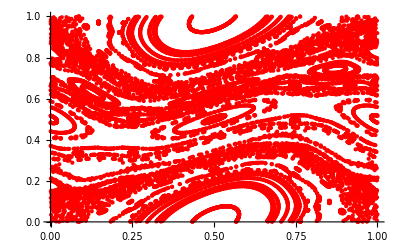

```mathematica
ListPlot[Table[Transpose[x[[i]]], {i,1,iter}],PlotStyle->Red]
```

## 並列計算

計算時間のボトルネックは計算時間がかかる順に

1. Fourier変換 (Evolve等々)

2. Unitary行列の構成 (Unitary等々)

3. 対角化 (Eigen等々)

4. BCH展開から行列の構成 (BCH`BCH2等々)

扱う問題が並列化可能かどうかは個別に議論しなくてはならない．
Fourier変換，対角化は恐らくこれ以上早くならないので並列化は試みない．
また，2. は並列化してもあまり速度が早くならかったので行わない．
4は関数のレベルで並列評価しているが，ユーザーが並列計算を意識する必要はない．

では，なぜ本章を設けたかと言うと，
ユーザーが意識すれば，多くの問題が並列化可能であるという事に気づいてほしいからである．
例えば複数の行列を求め，並列して対角化すれば全体の計算時間が短くなると言った具合である．
並列計算を実行する為に，ユーザーも多少並列計算の知識を必要とするが，必要となるMathematica関数は

```mathematica
LaunchKernels;
CloseKernels:
ParallelMap;
ParallelTable;
Names["Parallel*"]　(*他にもこんなものが有る程度に*)
```

{ParallelArray,ParallelCombine,ParallelDo,ParallelEvaluate,Parallelization,Parallelize,ParallelMap,ParallelNeeds,ParallelProduct,ParallelSubmit,ParallelSum,ParallelTable,ParallelTry}

である．
MapやTableは多くの場合，ParallelMap等に置き換えるだけで並列化が可能であるのでぜひ使ってみてほしい．
詳しくはDocumentation Centerで確認してほしい．

では実際に，調和振動子のハミルトニアン行列をあえてBCH展開の各次数毎に求め，並列してエネルギーを求めてみよう．

```mathematica
Exit[]
```

```mathematica
Get["Quantica`"];
LaunchKernels[2];
```

ここで，Kernelを起動させたが，LaunchKernelsを行わなければ使用できるKernelすべてを利用する．起動したKernelは

```mathematica
Kernels[]
```

{KernelObject[1,local],KernelObject[2,local]}

で確認できる．

```mathematica
Quantica`MP`dps=20;
T[x_]:=x^2/2
V[x_]:=x^2/2
dim=40;
domain={{-2,2},{-2,2}};
QuanticaSetting[dim,domain,tau->1/10,Verbose->True];
SetSystem[T,V];
matT=FourierBase`MatrixT[];
matV=FourierBase`MatrixV[];
A=-I*matT*Tau/Hbar;
B=-I*matV*Tau/Hbar;
```

{Dim:,40,Domain:,{{-2,2},{-2,2}},Tau:,1/10,dps:,20}

```mathematica
res=BCH`BCH3List[7,B/2,A,B/2,Verbose->True]; (*ちょっと時間が掛かる*)
(*{BCH[1,B/2,A,B/2],BCH[3,B/2,A,B/2], ..., BCH[7,B/2,A,B/2]}を得る．*)
```

{2 word Symmetric BCH series:,3}

{2 word Symmetric BCH series:,5}

{2 word Symmetric BCH series:,7}

```mathematica
mats=Table[Hbar*I*res[[i]]/Tau,{i,1,Length[res]}];
evals=ParallelEigen[mats,Vector->False];
evals=Table[evals[[i]]/Hbar,{i,1,Length[evals]}];
(* ファイルをtextに書き出す場合
For[i=1,i<=Length[evals],++i,Print[i];
fname="bch_energy_"<>ToString[2*i-1]<>".dat";
Util`SaveEigenvalue[evals[[i]],fname]
]
*)
```

複数の行列を対角化する為にParallelEigenを用意していますが，実態は
ParallelMap[Eigenvalues, mats]
を行っているだけです．これで複数の行列を並列して対角化する事が可能である．

計算結果を比較すると，

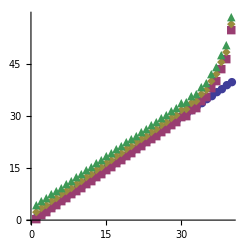

```mathematica
ref = Table[{i,i},{i,1,dim}];
ListPlot[{ref, evals[[1]],evals[[2]]+2,evals[[3]]+4},
PlotMarkers->{Automatic,Small},ImageSize->{245,245},AspectRatio->Full]
```

比較のためわずかにy軸方向に動かしている．